## Preliminary

```mathematica
SetDirectory[NotebookDirectory[]];
Timing[<<MERA`]
```

{0.021667,Null}

```mathematica
loadMERA["ising6.dat"]
```

## Problem 1

### Dimensions of w and u

Indeed w and u are a list of length Nlayers:

```mathematica
Length/@{w,u}
%=={Nlayers,Nlayers}
```

{6,6}

True

Every layer contains only one tensor, as this is a translationally invariant MERA, i.e. all tensors are assumed to be the same on a single layer”

```mathematica
{Length/@w,Length/@u}
```

{{1,1,1,1,1,1},{1,1,1,1,1,1}}

The dimensions of the legs on the lattice sites has to be 2 (it is the Ising model), and all other legs have dimension 6 (the bond dimension). Note that u and w hence have different dimensions on the first layer.

```mathematica
Dimensions/@w⟦;;,1⟧
Dimensions/@u⟦;;,1⟧
```

{{6,2,2,2},{6,6,6,6},{6,6,6,6},{6,6,6,6},{6,6,6,6},{6,6,6,6}}

{{2,2,2,2},{6,6,6,6},{6,6,6,6},{6,6,6,6},{6,6,6,6},{6,6,6,6}}

### Checking unitarity and isometries using sum

We first define the sums as presented in the figure, subtract the identity matrix and return the maximum deviation (expected to be of order 10^(-$MachinePrecision), i.e 10^-15:

```mathematica
checkiso[w_]:=Module[{dimsw=Dimensions[w]},
Table[Sum[w⟦μ,α,β,γ⟧ w⟦μpr,α,β,γ⟧*,{α,dimsw⟦2⟧},{β,dimsw⟦3⟧},{γ,dimsw⟦4⟧}],{μ,dimsw⟦1⟧},{μpr,dimsw⟦1⟧}]-IdentityMatrix[dimsw⟦1⟧]//Abs//Max
]
checkuni[u_]:=Module[{dimsu=Dimensions[u]},
Table[Sum[u⟦μ,ν,α,β⟧ u⟦μpr,νpr,α,β⟧*,{α,dimsu⟦3⟧},{β,dimsu⟦4⟧}],{μ,dimsu⟦1⟧},{μpr,dimsu⟦1⟧},{ν,dimsu⟦2⟧},{νpr,dimsu⟦2⟧}]-Outer[Times,IdentityMatrix[dimsu⟦1⟧],IdentityMatrix[dimsu⟦2⟧]]//Abs//Max
]
```

```mathematica
Timing[checkiso/@Flatten[w,1]]
Timing[checkuni/@Flatten[u,1]]
```

{0.10535,{1.55431×10^-15,8.88178×10^-16,8.88178×10^-16,8.88178×10^-16,8.88178×10^-16,8.88178×10^-16}}

{0.624751,{1.33227×10^-15,1.33227×10^-15,1.11022×10^-15,1.11022×10^-15,1.11022×10^-15,1.11022×10^-15}}

### Checking unitarity and isometries using ncon

Now the same sums using ncon. For illustrative purposes the outer product is also done using ncon. Note that the results are not exactly the same, the round off error in this case depends on the order of the summations. It is also clear that ncon is much more efficient than writing out the sum explicitly (ncon rewrites the sum into a dot-product, which Mathematica processes using much faster low-level processing).

```mathematica
checkiso2[w_]:=ncon[{w,w*},{{-1,1,2,3},{-2,1,2,3}}]-IdentityMatrix[Length[w]]//Abs//Max
checkuni2[u_]:=ncon[{u,u*},{{-1,-2,1,2},{-3,-4,1,2}}]-ncon[{IdentityMatrix[Length[u]],IdentityMatrix[Length[u]]},{{-1,-3},{-2,-4}}]//Abs//Max
```

```mathematica
Timing[checkiso2/@Flatten[w,1]]
Timing[checkuni2/@Flatten[u,1]]
```

{0.006501,{1.55431×10^-15,6.66134×10^-16,1.33227×10^-15,1.33227×10^-15,1.33227×10^-15,1.33227×10^-15}}

{0.01048,{1.33227×10^-15,1.33227×10^-15,1.33227×10^-15,1.33227×10^-15,1.33227×10^-15,1.33227×10^-15}}

### Consistency conditions of ncon

This answer of this excersize is basically in nconc. In summary it implements:
- check if tensors is actually a list of tensors (i.e. rectangular Arrays)
- check if all tensors have corresponding legs specified, with the right dimensions
- check if each leg connects exactly two tensors
- check if each leg contracts indices of the same dimension
- check if the left-over legs are numbered sequentially with negative numbers

### The energy density and spin expectation values

The first dens tensor represents a two-site density matrix, tracing out the rest of the network, which can be used to compute the expectation value of the magnetic field:

```mathematica
mag[dir_]:=ncon[{out[PauliMatrix[dir],IdentityMatrix[d]],dens⟦1,1⟧},{{3,1,4,2},{1,2,3,4}}]
```

```mathematica
mag/@Range[3]//Re
```

{-1.65141×10^-8,3.15469×10^-8,-0.636663}

At the critical point the spin chain is not yet spontaneously magnitized in the x direction.

```mathematica
hamiltonian=ncon[{PauliMatrix[3],IdentityMatrix[d]},{{-1,-3},{-2,-4}}]+ncon[{PauliMatrix[1],PauliMatrix[1]},{{-1,-3},{-2,-4}}]
```

{{{{1,0},{0,1}},{{0,1},{1,0}}},{{{0,1},{-1,0}},{{1,0},{0,-1}}}}

```mathematica
energy=ncon[{dens⟦1,1⟧,hamiltonian},{{1,2,3,4},{3,4,1,2}}]//Re
difwithanalytic=energy+4/π
relativeerror=%/(4/π)
```

-1.27324

2.36181×10^-6

1.85496×10^-6

The energy density agrees with the analytic answer upto 5 parts in a million, which is quite impressive for a critical system with a relatively low bond dimension of χ=6.

### Computational cost of tensor contractions

As one example, note that contracting legs 11 and 12 cost χ^6, because the two w’s have 4 open legs, and one needs to 2 summations for each element of the resulting rank 4-tensor. One fast sequence is listed below, its cost being 6 χ^6. When shifting the green operator the optimal cost becomes 2 χ^8+2 χ^7+2 χ^6.

```mathematica
findsequence[{{-1,1,2,3},{-3,1,2,9},{-2,4,11,12},{-4,10,11,12},{3,4,5,6},{7,8,9,10},{5,6,7,8}}]
```

cost found: {6000000,{3,4},{1,2,5,6,7},{1,2,3,4,5,6,7},12,1000000,{4,10}}

{11,12,5,6,7,8,1,2,3,9,4,10}

## 2. Scaling operators and entanglement

### Computing <σ_(x,1)σ_(x,4)> and <σ_(x,1)σ_(x,10)>

The diagram looks like this :

(figure to be inserted)

```mathematica
oo3=ncon[{PauliMatrix[1],PauliMatrix[1],w⟦1,1⟧,w⟦1,1⟧*,w⟦1,1⟧,w⟦1,1⟧*,dens⟦2,1⟧},{{2,3},{8,9},{5,1,2,4},{11,1,3,4},{6,7,8,10},{12,7,9,10},{11,12,5,6}}]//Re
```

taking trace

taking trace

-0.489235

For the 1 - 10 correlation we need one extra layer of isometries :

(figure to be inserted)

```mathematica
oo9=nconp[{PauliMatrix[1],PauliMatrix[1],w⟦1,1⟧,w⟦1,1⟧*,w⟦1,1⟧,w⟦1,1⟧*,w⟦2,1⟧,w⟦2,1⟧*,w⟦2,1⟧,w⟦2,1⟧*,dens⟦3,1⟧},{{2,3},{8,9},{5,1,2,4},{11,1,3,4},{6,7,8,10},{12,7,9,10},{13,14,5,15},{16,14,11,15},{19,17,6,18},{20,17,12,18},{16,20,13,19}}]//Re
```

taking trace

taking trace

taking trace

«1 more identical outputs»

total cost is 1χ^2 + 1χ^5 + 1χ^6 + 4χ^7 + 1χ^8 + 2χ^9  total: 10719684  (old: 23009220)

-0.372165

(taking trace is in fact a warning that the contraction sequence is sub-optimal; this can be improved by finding a faster sequence, in fact it can be done in χ^5, as opposed to the χ^9 done here, as outputted using nconp)

### Computing <σ_(x,1)σ_(x,28)> and checking if σ_x is a scaling operator

```mathematica
oo27=nconp[{PauliMatrix[1],PauliMatrix[1],w⟦1,1⟧,w⟦1,1⟧*,w⟦1,1⟧,w⟦1,1⟧*,w⟦2,1⟧,w⟦2,1⟧*,w⟦2,1⟧,w⟦2,1⟧*,w⟦3,1⟧,w⟦3,1⟧*,w⟦3,1⟧,w⟦3,1⟧*,dens⟦4,1⟧},{{2,3},{8,9},{5,1,2,4},{11,1,3,4},{6,7,8,10},{12,7,9,10},{13,14,5,15},{16,14,11,15},{19,17,6,18},{20,17,12,18},{23,21,13,22},{24,21,16,22},{28,25,19,26},{27,25,20,26},{24,27,23,28}}]//Re
```

taking trace

taking trace

taking trace

«3 more identical outputs»

total cost is 1χ^2 + 1χ^4 + 2χ^5 + 1χ^6 + 6χ^7 + 1χ^8 + 2χ^9  total: 11288628  (old: 23578164)

-0.282373

```mathematica
data={{3,oo3},{9,oo9},{27,oo27}};
CFTcor=a x^(-2Δ);
fit=FindFit[data//Abs,a x^(-2Δ),{a,Δ},x]
```

{a→0.643969,Δ→0.124962}

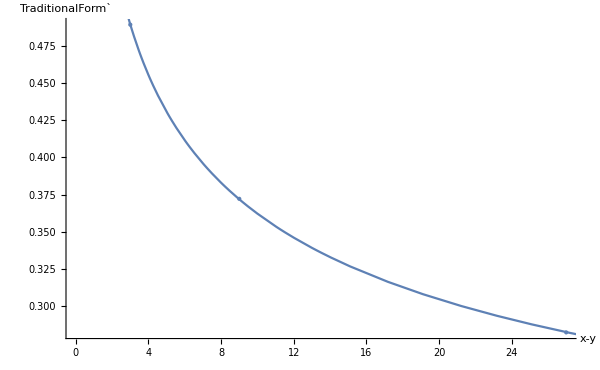

```mathematica
Show[ListPlot[{{3,oo3},{9,oo9},{27,oo27}}//Abs,PlotStyle->PointSize[Large],BaseStyle->20,ImageSize->600,AxesLabel->{"x-y","TraditionalForm`"}],Plot[CFTcor/.fit,{x,1,100},PlotRange->All,PlotLegends->Style[CFTcor/.fit,25]]]
```

Even though it is usually not a good idea to take a two parameter fit through three points, it is seen that it works remarkably well. In fact, the Ising spin operator is known to be a scaling operator of dimension 1/8, almost exactly as found here.

### Scaling operators from the spectrum of w

As was seen in the previous excersize, tripling the distance corresponds to adding one layer of w, just rescaling the operator. This is a linear operation on an operator (2-tensor), so we need to combine the legs to get a matrix of which we can compute the eigenvalues:

```mathematica
spectrum=Eigenvalues[ArrayReshape[ncon[{w⟦-1,1⟧,w⟦-1,1⟧*},{{-3,1,-1,2},{-4,1,-2,2}}],{χ^2,χ^2}]]//Abs
```

{1.,0.871054,0.327487,0.296339,0.286034,0.122818,0.121941,0.121941,0.110741,0.108655,0.095558,0.0817534,0.0637686,0.062831,0.0541924,0.0456533,0.0389634,0.0375625,0.0353224,0.0351287,0.0254211,0.0197831,0.0176716,0.0176716,0.0176025,0.0173855,0.0118832,0.00935772,0.00861565,0.00736681,0.00591627,0.00489042,0.00470425,0.00470425,0.00283178,0.00280576}

The eigenvalues are related to the scaling dimension through the following formula :

{-4.24439×10^-15,0.12566,1.01611,1.10708,1.1393,1.90882,1.91535,1.91535,2.00304,2.02035,2.13726,2.27928,2.50543,2.51891,2.65354,2.80962,2.95385,2.98718,3.04315,3.04815,3.34256,3.5708,3.67354,3.67354,3.67711,3.6884,4.03475,4.25223,4.32744,4.46998,4.66957,4.84291,4.87823,4.87823,5.34024,5.34864}

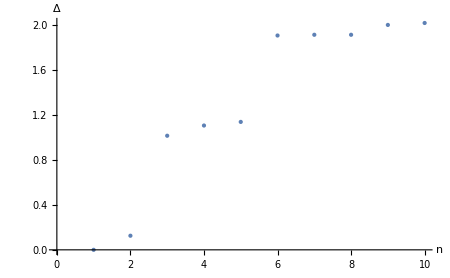

```mathematica
scalingdimensions=-Log[3,spectrum]
ListPlot[%⟦;;10⟧,PlotStyle->PointSize[Large],BaseStyle->20,ImageSize->450,AxesLabel->{"n","Δ"}]
```

### Reduced density matrix and entropy

The reduced density matrix is a bit more complicated, one has to be especially careful to arrange the order of the legs with each tensor properly. This requires a bit of drawing. The reduced density matrix for 8 sites looks like :

-Graphics-

```mathematica
Dimensions[ρred2=nconp[{w⟦1,1⟧,w⟦1,1⟧*,w⟦1,1⟧,w⟦1,1⟧*,dens⟦2,1⟧},{{3,2,1,-1},{4,2,1,-3},{7,-2,5,6},{8,-4,5,6},{4,8,3,7}}]]
```

total cost is 4χ^6  total: 6912  (old: 186624)

{2,2,2,2}

```mathematica
spectrum=Eigenvalues[ArrayReshape[ρred2,{4,4}]]//Abs
{EEL2,RenyiL2}={-Tr[spectrum Log[spectrum]],-Log[Tr[spectrum^2]]}
```

{0.767706,0.220951,0.00880238,0.0025407}

{0.593377,0.448984}

```mathematica
Dimensions[ρred8=nconp[{w⟦1,1⟧,w⟦1,1⟧*,w⟦1,1⟧,w⟦1,1⟧*,w⟦2,1⟧,w⟦2,1⟧*,w⟦2,1⟧,w⟦2,1⟧*,dens⟦3,1⟧},{{3,2,1,-1},{4,2,1,-5},{7,-4,5,6},{8,-8,5,6},{10,9,3,-2},{11,9,4,-6},{13,-3,7,12},{14,-7,8,12},{11,14,10,13}}]]
```

taking trace

taking trace

total cost is 2χ^6 + 2χ^7 + 1χ^8 + 2χ^9 + 1χ^10  total: 3235968  (old: 82954368)

{2,6,6,2,2,6,6,2}

```mathematica
spectrum=Eigenvalues[ArrayReshape[ρred8,{4 6^2,4 6^2}]]//Abs;
{EEL8,RenyiL8}={-Tr[spectrum Log[spectrum]],-Log[Tr[spectrum^2]]}
```

{0.825071,0.63184}

### Renyi entropy directly and central charge

```mathematica
-Log[ncon[{ρred2,ρred2},{{1,2,3,4},{1,2,3,4}}]]
```

0.456003+4.17457×10^-17 ⅈ

```mathematica
renyi2=-Log[ncon[{ρred2,ρred2},{{1,2,3,4},{3,4,1,2}}]]//Re
renyi8=-Log[ncon[{ρred8,ρred8},{{1,2,3,4,5,6,7,8},{5,6,7,8,1,2,3,4}}]]//Re
```

0.448984

0.63184

```mathematica
centralcharge=FindFit[{{2,renyi2},{8,renyi8}},c/4 Log[l]+const,{c,const},l]
```

{c→0.527609,const→0.357557}

Not a bad result for a computation so close to the lattice cut-off. More reliable estimates can be obtained by comparing the Renyi’s at long distances (the entanglement entropy can unfortunately not be computed efficiently there)

#### (Optional) a few more Renyis:

Computing Renyis till L=3^10-1 gives a more accurate central charge estimate:

```mathematica
renyL2[lay_]:=Monitor[
ϕ2=ncon[{IdentityMatrix[d],IdentityMatrix[d]},{{-1,-2},{-3,-4}}];
ϕ2R=ncon[{IdentityMatrix[d],IdentityMatrix[d]},{{-1,-2},{-3,-4}}];
Table[
layI=Min[i,Nlayers];
ϕ2=ncon[{w⟦layI,1⟧,w⟦layI,1⟧*,w⟦layI,1⟧,w⟦layI,1⟧*,ϕ2},{{-1,2,5,1},{-2,2,6,3},{-3,4,7,3},{-4,4,8,1},{5,6,7,8}},{5,1,8,4,7,2,3,6}];
ϕ2R=ncon[{w⟦layI,1⟧,w⟦layI,1⟧*,w⟦layI,1⟧,w⟦layI,1⟧*,ϕ2R},{{-1,1,5,2},{-2,3,6,2},{-3,3,7,4},{-4,1,8,4},{5,6,7,8}},{5,1,8,4,7,2,3,6}];
-Log[ncon[{ϕ2,dens⟦Min[i+1,Nlayers+1],1⟧,ϕ2R,dens⟦Min[i+1,Nlayers+1],1⟧},{{3,1,5,6},{1,2,3,4},{4,2,7,8},{6,8,5,7}},{6,5,8,7,1,3,4,2}]]
,{i,lay}]
,i]
```

```mathematica
renyL2[10]//Re
```

{0.448984,0.63184,0.781405,0.922542,1.06113,1.1989,1.3364,1.47381,1.61119,1.74857}

```mathematica
centralcharge:=
(Timing[renys2=renyL2[10]//Chop];
Solve[c/4 Log[3]==renys2⟦-1⟧-renys2⟦-2⟧,c]⟦1⟧)
```

```mathematica
centralcharge
```

{c→0.500168}